n: 5

pts: {{0,0.93},{1,0.75},{0,0.57},{1,0.39},{0,0.21},{1,0.03}}

Last point = {1,0.03}

right wall

floor point= {0.833333,0}

new start point= {0,0.15}

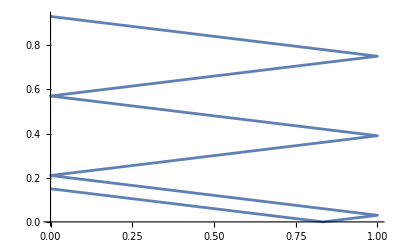

n: 5

pts: {{0,0.15},{1,0.33},{0,0.51},{1,0.69},{0,0.87}}

Last point = {0,0.87}

left wall

ceiling point= {0.722222,1}

new start point= {1,0.95}

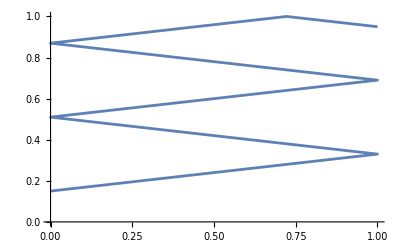

```mathematica
reboundsup[startpt_, m_]:=(
a = startpt[[2]];
(*larger if statement to account for whether it is going up or down*)
n=Ceiling[(1-a)/m];
Print["n: ", n]; (*debugging*)

If[startpt[[1]]==0,
(* if start point is on left wall *)
pts=Join[{startpt},Table[{((-1)^(k-1)+1)/2,a+ k*m},{k,1,n-1}]], 
(* else: if start point is on right wall *)
pts=Join[{startpt},Table[{((-1)^k+1)/2,a+ k*m},{k,1,n-1}]]];
Print["pts: ", pts]; (*debugging*)


(* change the direction here from up to down or down to up *)
lastpt = Last[pts];
Print["Last point = ", lastpt];
If[lastpt[[1]] ==0,
Print["left wall"];
ceilingpt={(1-lastpt[[2]])/m,1};
newstartpt = {1,1-m(1-ceilingpt[[1]])},

ceilingpt={(lastpt[[2]]-1+m)/m,1};
newstartpt = {0,1-m(ceilingpt[[1]])}];

Print["ceiling point= ", ceilingpt];
Print["new start point= ",newstartpt];
pts=Join[pts, {ceilingpt, newstartpt}]
(*Return[ newstartpt];*));


reboundsdown[startpt_, m_]:=(
a = startpt[[2]];
(*larger if statement to account for whether it is going up or down*)
n=Floor[(a)/m];
Print["n: ", n]; (*debugging*)

If[startpt[[1]]==0,
(* if start point is on left wall *)
pts=Join[{startpt},Table[{((-1)^(k-1)+1)/2,a- k*m},{k,1,n}]], 
(* else: if start point is on right wall *)
pts=Join[{startpt},Table[{((-1)^k+1)/2,a- k*m},{k,1,n}]]];
Print["pts: ", pts]; (*debugging*)

lastpt = Last[pts];
Print["Last point = ", lastpt];
If[lastpt[[1]] ==0,
Print["left wall"];
floorpt={(m * lastpt[[1]] +lastpt[[2]])/m,0};
newstartpt = {1,m(1-floorpt[[1]])},

Print["right wall"];
floorpt={(m*lastpt[[1]]-lastpt[[2]])/m,0};
newstartpt = {0,m*floorpt[[1]] }];

Print["floor point= ", floorpt];
Print["new start point= ",newstartpt];
pts=Join[pts, {floorpt, newstartpt}]);
ListLinePlot[reboundsdown[{0, .93}, .18]]
ListLinePlot[reboundsup[{0,.15}, .18]]
```